Зададим исходные данные

```mathematica
f[x_,y_]:=x^2+y^2;
x0=0;
y0=0;
b=1;
```

Построим разбиение отрезка, на котором ищется решение данной задачи Коши

```mathematica
n=10;
h=(b-x0)/n;
X=Table[x0+(k-1)*h,{k,1,n+1}];
```

Реализуем алгоритм метода Эйлера

```mathematica
Y=Table[0,{k,1,n+1}];
Y[[1]]=y0;
For[k=2,k≤n+1,k++,Y[[k]]=Y[[k-1]]+h*f[X[[k-1]],Y[[k-1]]]]
```

Выполним интерполяцию найденного приближенного решения задачи Коши и построим его график

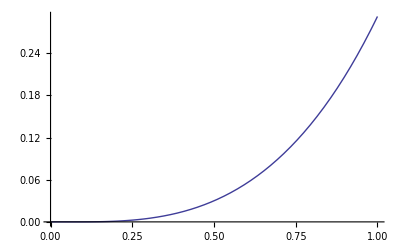

```mathematica
XY=Table[{X[[k]],Y[[k]]},{k,1,n+1}];
y=Interpolation[XY];
G=Plot[y[x],{x,x0,b}]
```